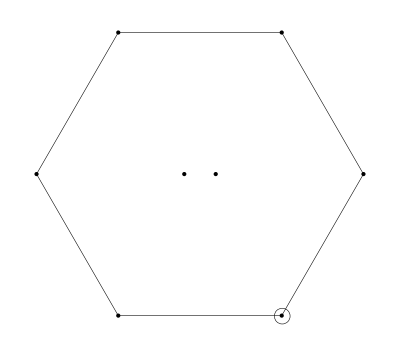

Y=-1.5,  I_3=0.5

(us+su)(ūd̄+d̄ū)+2ss(s̄d̄+d̄s̄)+2(sd+ds)d̄d̄

```mathematica
(*-------------------------------*)
```

The current J:

(s_a^T C1 u_b+u_a^T C1 s_b) ((d̄)_a 1C((ū)_b)^T)+(s_a^T C1 u_b+u_a^T C1 s_b) ((d̄)_b 1C((ū)_a)^T)+(s_a^T C1 u_b+u_a^T C1 s_b) ((ū)_a 1C((d̄)_b)^T)+(s_a^T C1 u_b+u_a^T C1 s_b) ((ū)_b 1C((d̄)_a)^T)+2 ((d̄)_a 1C((d̄)_b)^T) (d_a^T C1 s_b+s_a^T C1 d_b)+2 ((d̄)_b 1C((d̄)_a)^T) (d_a^T C1 s_b+s_a^T C1 d_b)+2 (s_a^T C1 s_b) ((d̄)_a 1C((s̄)_b)^T+(d̄)_b 1C((s̄)_a)^T)+2 (s_a^T C1 s_b) ((s̄)_a 1C((d̄)_b)^T+(s̄)_b 1C((d̄)_a)^T)

the Fierz rearranged J (to naively get the decay partten)

```mathematica
2 (d̄(γ^μ).(γ̄)^5 d d̄(γ^μ).(γ̄)^5 s)+2 (d̄(γ^μ).(γ̄)^5 s s̄(γ^μ).(γ̄)^5 s)+2 (d̄ γ^μ d d̄ γ^μ s)+2 (d̄ γ^μ s s̄ γ^μ s)-2 (d̄(γ̄)^5 s) (d̄(γ̄)^5 d+s̄(γ̄)^5 s)+d̄ σ^μν d d̄ σ^μν s+d̄ σ^μν s s̄ σ^μν s+d̄(γ^μ).(γ̄)^5 s ū(γ^μ).(γ̄)^5 u+d̄(γ^μ).(γ̄)^5 u ū(γ^μ).(γ̄)^5 s+d̄ γ^μ s ū γ^μ u+d̄ γ^μ u ū γ^μ s-d̄(γ̄)^5 s ū(γ̄)^5 u-d̄(γ̄)^5 u ū(γ̄)^5 s+1/2 (d̄ σ^μν s ū σ^μν u)+1/2 (d̄ σ^μν u ū σ^μν s)-d̄ 1s ū 1u-d̄ 1u ū 1s-2 (d̄ 1s) (d̄ 1d+s̄ 1s)
```

Π(q^2)=
-(log(-q^2/μ^2) q^8)/(384 π^6)+(5 ⟨ GG ⟩ log(-q^2/μ^2) q^4)/(96 π^5)-(⟨ ū u⟩ log(-q^2/μ^2) (m_d+m_s+m_u) q^4)/(6 π^4)-(⟨ d̄ d⟩ log(-q^2/μ^2) (17 m_d+8 m_s+2 m_u) q^4)/(12 π^4)-(⟨ s̄ s⟩ log(-q^2/μ^2) (8 m_d+17 m_s+2 m_u) q^4)/(12 π^4)-(2 ⟨ ū u⟩^2 log(-q^2/μ^2) q^2)/(3 π^2)+(25 ⟨G^3⟩ log(-q^2/μ^2) q^2)/(864 π^6)-(4 ⟨ d̄ d⟩ ⟨ ū u⟩ log(-q^2/μ^2) q^2)/(3 π^2)-(4 ⟨ s̄ s⟩ ⟨ ū u⟩ log(-q^2/μ^2) q^2)/(3 π^2)-(4 ⟨ d̄ d⟩ ⟨ d̄ Gd⟩ log(-q^2/μ^2))/(3 π^2)-(4 ⟨ s̄ s⟩ ⟨ d̄ Gd⟩ log(-q^2/μ^2))/(3 π^2)-(4 ⟨ d̄ d⟩ ⟨ s̄ Gs⟩ log(-q^2/μ^2))/(3 π^2)-(4 ⟨ s̄ s⟩ ⟨ s̄ Gs⟩ log(-q^2/μ^2))/(3 π^2)+(⟨ ū u⟩ ⟨ ū Gu⟩ log(-q^2/μ^2))/(3 π^2)-(10 ⟨ GG ⟩ ⟨ d̄ d⟩^2)/(9 π q^2)-(10 ⟨ GG ⟩ ⟨ s̄ s⟩^2)/(9 π q^2)-(2 ⟨ GG ⟩ ⟨ ū u⟩^2)/(9 π q^2)+(127 ⟨ d̄ Gd⟩^2)/(288 π^2 q^2)+(127 ⟨ s̄ Gs⟩^2)/(288 π^2 q^2)-⟨ ū Gu⟩^2/(96 π^2 q^2)-(20 ⟨ GG ⟩ ⟨ d̄ d⟩ ⟨ s̄ s⟩)/(9 π q^2)-(⟨ GG ⟩ ⟨ d̄ d⟩ ⟨ ū u⟩)/(π q^2)-(⟨ GG ⟩ ⟨ s̄ s⟩ ⟨ ū u⟩)/(π q^2)+(127 ⟨ d̄ Gd⟩ ⟨ s̄ Gs⟩)/(144 π^2 q^2)+(115 ⟨ d̄ Gd⟩ ⟨ ū Gu⟩)/(576 π^2 q^2)+(115 ⟨ s̄ Gs⟩ ⟨ ū Gu⟩)/(576 π^2 q^2)-(8 ⟨ d̄ d⟩ ⟨ s̄ s⟩^2 (16 m_d-16 m_s))/(9 q^2)-(32 ⟨ s̄ s⟩^2 ⟨ ū u⟩ (2 m_d+m_s))/(9 q^2)-(32 ⟨ d̄ d⟩^2 ⟨ ū u⟩ (m_d+2 m_s))/(9 q^2)-(8 ⟨ d̄ d⟩^2 ⟨ s̄ s⟩ (16 m_s-16 m_d))/(9 q^2)-(2 ⟨ d̄ d⟩ ⟨ ū u⟩^2 (4 m_d-8 m_s-8 m_u))/(9 q^2)-(2 ⟨ s̄ s⟩ ⟨ ū u⟩^2 (-8 m_d+4 m_s-8 m_u))/(9 q^2)-(8 ⟨ d̄ d⟩ ⟨ s̄ s⟩ ⟨ ū u⟩ (10 m_d+10 m_s-8 m_u))/(9 q^2)

```mathematica
(*-------------------------------*)
```

ℳ^0(s_0) for η_6=η_8=η_10=1

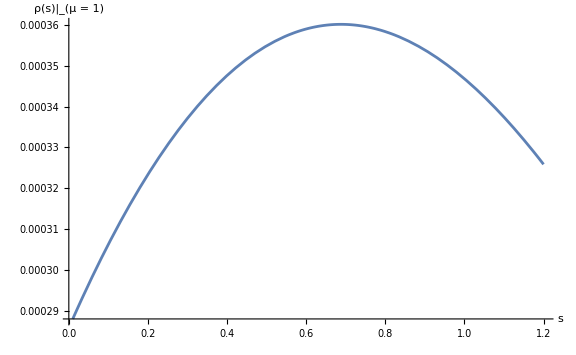
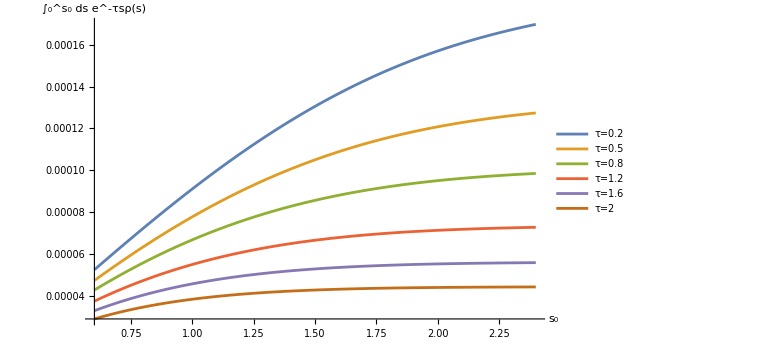

```mathematica
(*-------------------------------*)
```

(∫_0^s_0 dsC^i (s) ⟨𝒪_i⟩)/(∫_0^s_0 dsC^0 (s)) for η_6=η_8=η_10=1

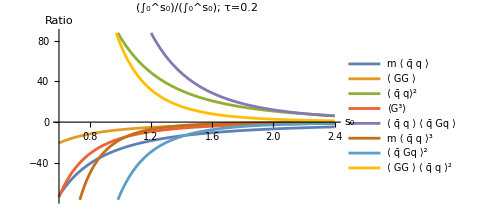
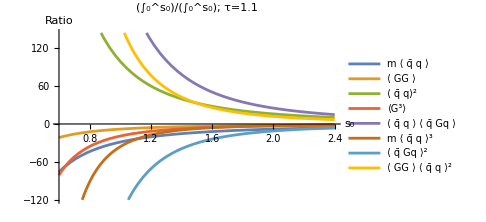
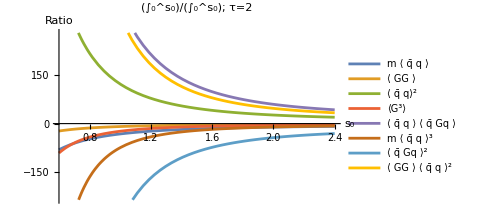

```mathematica
(*-------------------------------*)
```

ℛ^0 for η_6=η_8=η_10=1

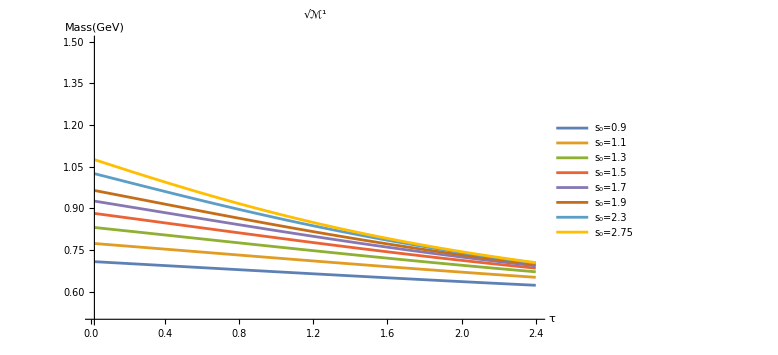
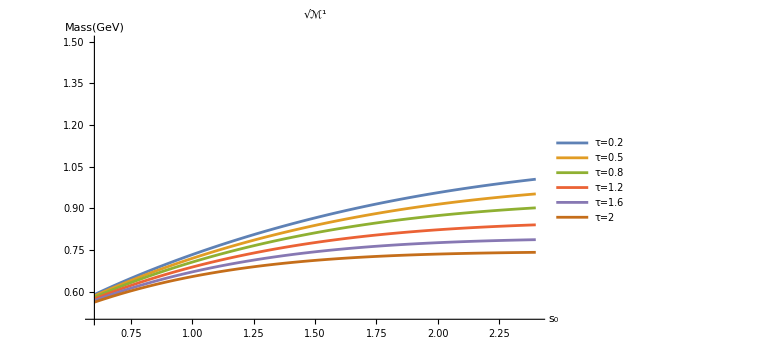

```mathematica
(*-------------------------------*)
```

ℛ^1 for η_6=η_8=η_10=1

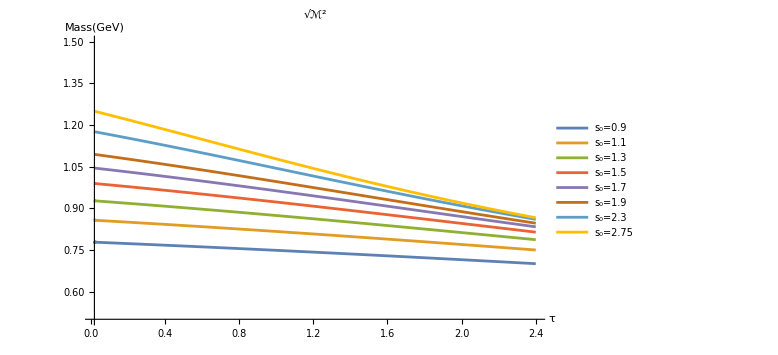
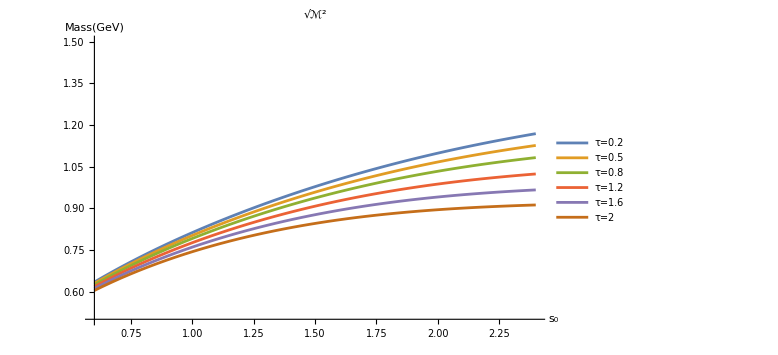

```mathematica
(*-------------------------------*)
```

ℳ^0(s_0) for η_6=3, η_8=5, η_10=5

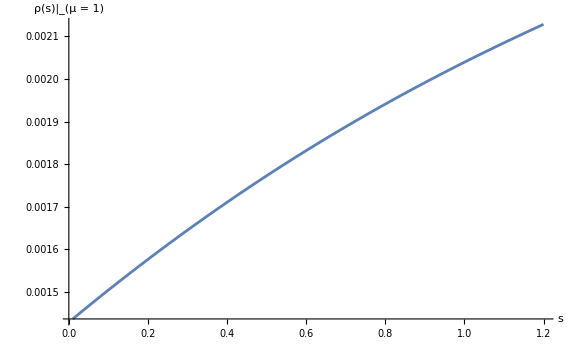
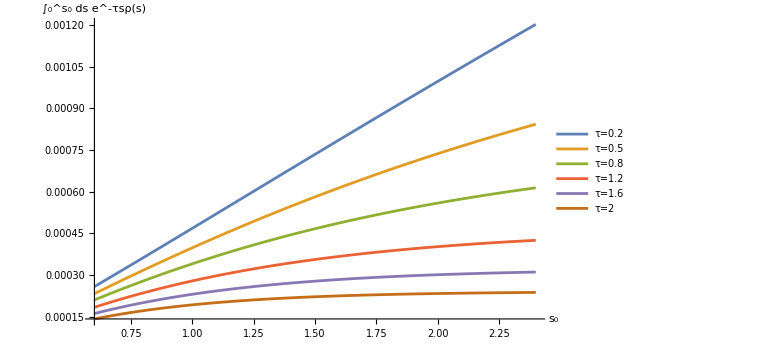

```mathematica
(*-------------------------------*)
```

(∫_0^s_0 dsC^i (s) ⟨𝒪_i⟩)/(∫_0^s_0 dsC^0 (s)) for η_6=3, η_8=5, η_10=5

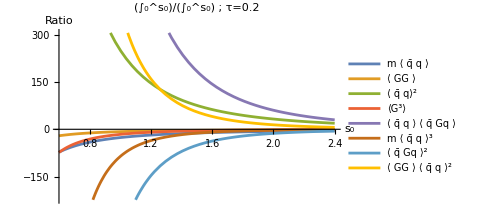
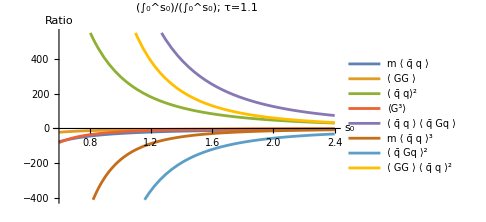
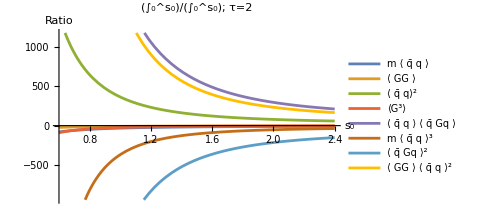

```mathematica
(*-------------------------------*)
```

ℛ^0 for η_6=3, η_8=5, η_10=5

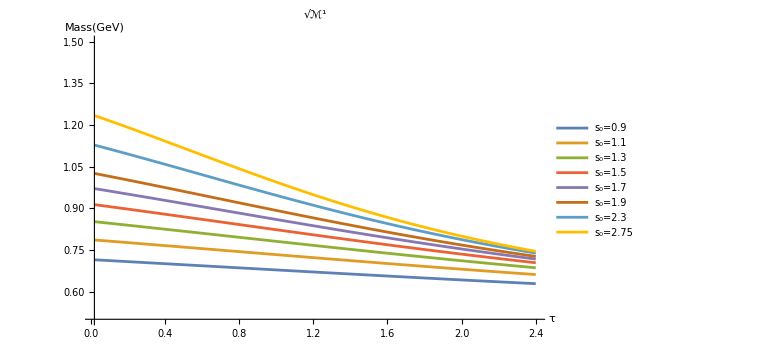
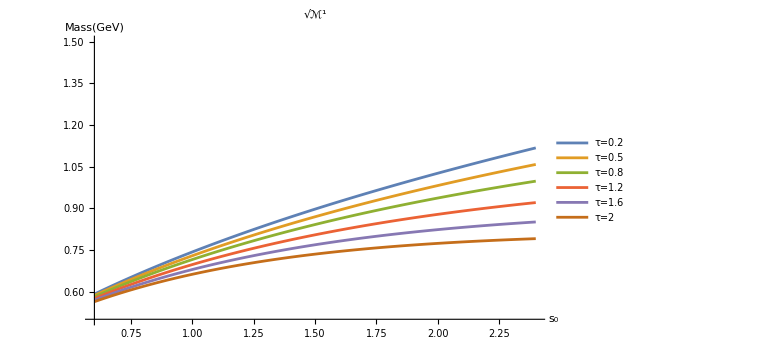

```mathematica
(*-------------------------------*)
```

ℛ^1 for η_6=3, η_8=5, η_10=5